# Basic 3D graphics

Math 250 - Mathematical Computing
Christopher Hanusa

## 10.1 Overview

In this tutorial, we start working with 3D graphics objects that are the analogues of their 2D counterparts.

## 10.2 Graphics3D and you’re good to go.

The major difference is that instead of using Graphics, you use Graphics3D to tell Mathematica that your object is a 3D object.
Once you change your (x,y)-coordinates to (x,y,z)-coordinates, you can re-use many of the 2D commands you learned, including Point, Line, BSplineCurve, and Polygon.

## 10.3 Points (0D)

### Points

```mathematica
{Graphics[Point[{0,0}]],Graphics3D[Point[{0,0,0}]]}
```

{-Graphics-,-Graphics3D-}

You can compare the following code with the 2D graphics code from the previous tutorial:

```mathematica
pointlist={{0,0,0},{1,1,0},{2,0,0},{3,1,0},{4,0,0},{5,1,0},{6,0,0},{7,1,0},{8,0,0}};
Graphics3D[Map[Point,pointlist]]
```

-Graphics3D-

### Spheres

To display a point in space, you can use the Point command, but instead you’ll probably want to use the Sphere command or Ball.

```mathematica
?Sphere
```

Here is a bunch of spheres all lined up.

```mathematica
Graphics3D[Table[Sphere[{i,0,0},.2],{i,0,10}]]
```

-Graphics3D-

Example 10.3.1. Use the Map command to put a sphere at a given set of coordinates:

```mathematica
spherelist=Map[Sphere[#,.2]&,pointlist];
Graphics3D[spherelist]
```

-Graphics3D-

## 10.4 Line Segments (1D)

The easiest way to take a 1D object like Line and make it 3-dimensional is to use the Tube command, which acts like a Line command, taking as input a sequence of points and creating a cylindrical path along the specified line segments that connect adjacent sets of points.

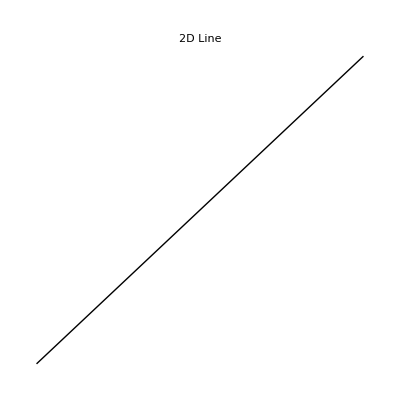
{-Graphics-,-Graphics3D-,-Graphics3D-}

```mathematica
{Graphics[Line[{{0,0},{1,1}}],PlotLabel->"2D Line"],
Graphics3D[Line[{{0,0,0},{1,1,1}}],PlotLabel->"3D Line"],
Graphics3D[Tube[{{0,0,0},{1,1,1}},.05],PlotLabel->"3D Tube"]}
```

```mathematica
zigzag=Graphics3D[Tube[pointlist,.2]]
```

-Graphics3D-

Unfortunately, the line segments created by this pure Tube object are not exportable to be 3D printed!  However, the concept of a Tube will be used to create 3D curves in the next tutorial.

## 10.5 Polygons (2D)

Just like in 2D Graphics, you can create polygons in three dimensions.  Remember to wrap it in a Graphics3D command.

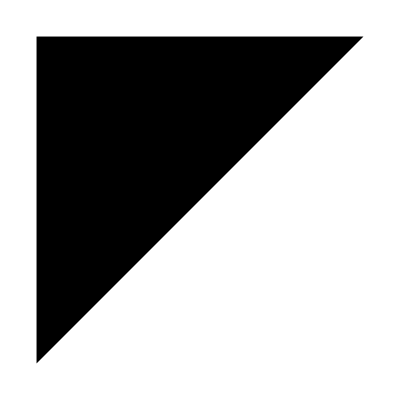
{-Graphics-,-Graphics3D-}

```mathematica
{Graphics[Polygon[{{0,0},{1,1},{0,1}}]],Graphics3D[Polygon[{{0,0,0},{1,1,1},{0,1,1/2}}]]}
```

## 10.6 Polyhedra (3D)

A polyhedron can be thought of as the three-dimensional analog of a polygon.  (And the plural of polyhedron is polyhedra!!)  The corners are called vertices, line segments connecting vertices are called edges, and the 2-D polygons are called faces.  Mathematica has a large number of built-in polyhedra, accessible using the command PolyhedronData.

```mathematica
Length[PolyhedronData[All]]
```

203

For example, here is a visualization of the 20-sided polyhedron called an icosohedron.

```mathematica
Graphics3D[{PolyhedronData["Icosahedron","Faces"]}]
```

-Graphics3D-

Copied directly from the Mathematica Documentation Center, here is an explorer of the polyhedra that Mathematica has built in along with their properties:

```mathematica
Manipulate[Column[{PolyhedronData[g],PolyhedronData[g,p]}],{g,PolyhedronData[All]},{p,Complement@@PolyhedronData/@{"Properties","Classes"}}]
```

## 10.7 Other 3D primitives

There are other basic 3D shapes available in Mathematica.  Unfortunately many of them are not exportable to be 3D printed.  Mathematica developers are working to improve this functionality.  Except for Cuboid, don’t use these in your project.

```mathematica
Graphics3D[Cuboid[]]
```

-Graphics3D-

```mathematica
Map[Graphics3D,{Tetrahedron[],Cylinder[],Cone[],Parallelepiped[],CapsuleShape[]}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

See more in guide/GeometricSpecialRegions.